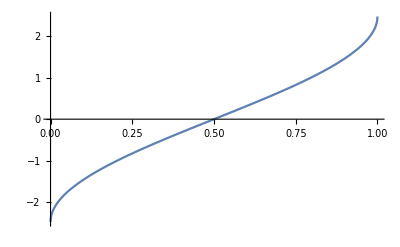

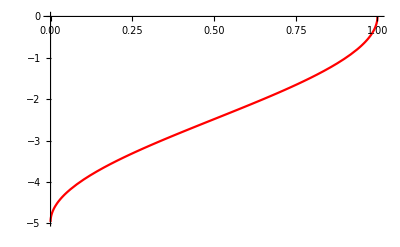

```mathematica
a = 0.1; t0 = 2;
MarL[x_]=(1/Sqrt[2*a*t0])*ArcSin[2*x-1];
RenL[x_]=-Sqrt[2/(a*t0)]*ArcSin[Sqrt[1-x]];
P1=Plot[MarL[x],{x,0,1},PlotLegends->Automatic]
P2=Plot[RenL[x],{x,0,1},PlotStyle->Red,PlotLegends->"Expressions"]
```

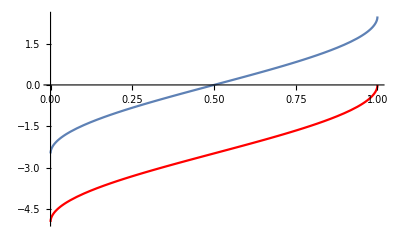

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/new_model/Lamp_Comp.pdf

```mathematica
S = Show[P1,P2,PlotRange->All]
Export[NotebookDirectory[]<>"Lamp_Comp.pdf",S]
```